## Seasonal Ricker model - EWS in rb - Intervals

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal2"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=0;
bh=2.24;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="ricker_trans_rb_temp";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

3

```mathematica
(* Realisation number to display *)
displayNum=1;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

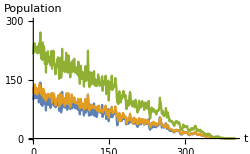

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB,seriesTotal},
Joined->True,
ImageSize->250,
LabelStyle->12,
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},{0,300}}]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.5];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

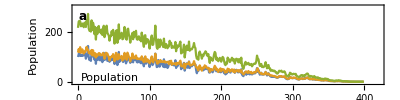

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,300}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Harvesting effort, F"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (Mean +/- SD)

### Variance

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Construct relevant sub dataframe *)
varEws=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{realNum,state,_,_}][[;;,{3,4}]],
{_,""}],
{realNum,1,numSims},{state,stateVals}];
```

```mathematica
varEws//Dimensions
```

{3,3,212,2}

```mathematica
(* Compute intervals *)
timeVals=varEws[[1,1,;;,1]];
varEwsMean=Mean[varEws[[;;,;;,;;,2]]];
varEwsSD=StandardDeviation[varEws[[;;,;;,;;,2]]];
```

```mathematica
plotVarB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[1]]-varEwsSD[[1]],varEwsMean[[1]],varEwsMean[[1]]+varEwsSD[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarNB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[2]]-varEwsSD[[2]],varEwsMean[[2]],varEwsMean[[2]]+varEwsSD[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarTot=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[3]]-varEwsSD[[3]],varEwsMean[[3]],varEwsMean[[3]]+varEwsSD[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

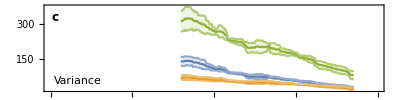

```mathematica
(* Plot variance EWS for display param *)
plotVar=Show[{plotVarB,plotVarNB,plotVarTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Construct relevant sub dataframe *)
skewEws=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{realNum,state,_,_}][[;;,{3,4}]],
{_,""}],
{realNum,1,numSims},{state,stateVals}];
```

```mathematica
(* Compute intervals *)
timeVals=skewEws[[1,1,;;,1]];
varEwsMean=Mean[skewEws[[;;,;;,;;,2]]];
varEwsSD=StandardDeviation[skewEws[[;;,;;,;;,2]]];
```

```mathematica
plotVarB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[1]]-varEwsSD[[1]],varEwsMean[[1]],varEwsMean[[1]]+varEwsSD[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarNB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[2]]-varEwsSD[[2]],varEwsMean[[2]],varEwsMean[[2]]+varEwsSD[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarTot=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[3]]-varEwsSD[[3]],varEwsMean[[3]],varEwsMean[[3]]+varEwsSD[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

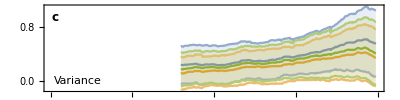

```mathematica
(* Plot variance EWS for display param *)
plotSkew=Show[{plotVarB,plotVarNB,plotVarTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
cvEws=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{realNum,state,_,_}][[;;,{3,4}]],
{_,""}],
{realNum,1,numSims},{state,stateVals}];
```

```mathematica
(* Compute intervals *)
timeVals=varEws[[1,1,;;,1]];
cvEwsMean=Mean[cvEws[[;;,;;,;;,2]]];
cvEwsSD=StandardDeviation[cvEws[[;;,;;,;;,2]]];
```

```mathematica
plotCvB=ListLinePlot[Transpose[{timeVals,#}]&/@{cvEwsMean[[1]]-cvEwsSD[[1]],cvEwsMean[[1]],cvEwsMean[[1]]+cvEwsSD[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotCvNB=ListLinePlot[Transpose[{timeVals,#}]&/@{cvEwsMean[[2]]-cvEwsSD[[2]],cvEwsMean[[2]],cvEwsMean[[2]]+cvEwsSD[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotCvTot=ListLinePlot[Transpose[{timeVals,#}]&/@{cvEwsMean[[3]]-cvEwsSD[[3]],cvEwsMean[[3]],cvEwsMean[[3]]+cvEwsSD[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

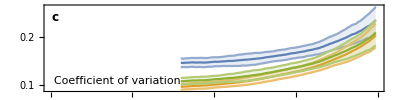

```mathematica
(* Plot variance EWS for display param *)
plotCv=Show[{plotCvB,plotCvNB,plotCvTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxEws=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{realNum,state,_,_}][[;;,{3,4}]],
{_,""}],
{realNum,1,numSims},{state,stateVals}];
```

```mathematica
(* Compute intervals *)
timeVals=smaxEws[[1,1,;;,1]];
varEwsMean=Mean[smaxEws[[;;,;;,;;,2]]];
varEwsSD=StandardDeviation[smaxEws[[;;,;;,;;,2]]];
```

```mathematica
plotVarB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[1]]-varEwsSD[[1]],varEwsMean[[1]],varEwsMean[[1]]+varEwsSD[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarNB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[2]]-varEwsSD[[2]],varEwsMean[[2]],varEwsMean[[2]]+varEwsSD[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarTot=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[3]]-varEwsSD[[3]],varEwsMean[[3]],varEwsMean[[3]]+varEwsSD[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

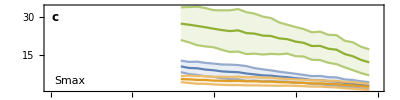

```mathematica
(* Plot variance EWS for display param *)
plotSmax=Show[{plotVarB,plotVarNB,plotVarTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{realNum,state,_,_}][[;;,{3,4}]],
{_,""}],
{realNum,1,numSims},{state,stateVals}];
```

```mathematica
(* Compute intervals *)
timeVals=smaxEws[[1,1,;;,1]];
varEwsMean=Mean[smaxVarEws[[;;,;;,;;,2]]];
varEwsSD=StandardDeviation[smaxVarEws[[;;,;;,;;,2]]];
```

```mathematica
plotVarB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[1]]-varEwsSD[[1]],varEwsMean[[1]],varEwsMean[[1]]+varEwsSD[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarNB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[2]]-varEwsSD[[2]],varEwsMean[[2]],varEwsMean[[2]]+varEwsSD[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarTot=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[3]]-varEwsSD[[3]],varEwsMean[[3]],varEwsMean[[3]]+varEwsSD[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

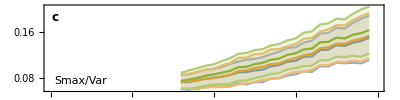

```mathematica
(* Plot variance EWS for display param *)
plotSmaxVar=Show[{plotVarB,plotVarNB,plotVarTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
ac1Ews=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{realNum,state,_,_}][[;;,{3,4}]],
{_,""}],
{realNum,1,numSims},{state,stateVals}];
```

```mathematica
(* Compute intervals *)
timeVals=ac1Ews[[1,1,;;,1]];
varEwsMean=Mean[ac1Ews[[;;,;;,;;,2]]];
varEwsSD=StandardDeviation[ac1Ews[[;;,;;,;;,2]]];
```

```mathematica
plotVarB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[1]]-varEwsSD[[1]],varEwsMean[[1]],varEwsMean[[1]]+varEwsSD[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarNB=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[2]]-varEwsSD[[2]],varEwsMean[[2]],varEwsMean[[2]]+varEwsSD[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotVarTot=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean[[3]]-varEwsSD[[3]],varEwsMean[[3]],varEwsMean[[3]]+varEwsSD[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

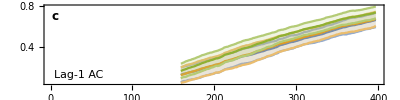

```mathematica
(* Plot variance EWS for display param *)
plotAc=Show[{plotVarB,plotVarNB,plotVarTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
varEws//Dimensions
```

{100,3,239,2}

```mathematica
ktauVar=Table[
KendallTau[DeleteCases[varEws[[realNum,state]],{_,""}][[;;,1]],DeleteCases[varEws[[realNum,state]],{_,""}][[;;,2]]],
{state,1,Length[stateVals]},{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVar,If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
varEws//Dimensions
```

{100,3,239,2}

```mathematica
ktauSkew=Table[
KendallTau[DeleteCases[skewEws[[realNum,state]],{_,""}][[;;,1]],DeleteCases[skewEws[[realNum,state]],{_,""}][[;;,2]]],
{state,1,Length[stateVals]},{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauSkew,If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
ktauCv=Table[
KendallTau[DeleteCases[cvEws[[realNum,state]],{_,""}][[;;,1]],DeleteCases[cvEws[[realNum,state]],{_,""}][[;;,2]]],
{state,1,Length[stateVals]},{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauCv,If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
ktauSmaxVar=Table[
KendallTau[DeleteCases[smaxVarEws[[realNum,state]],{_,""}][[;;,1]],DeleteCases[smaxVarEws[[realNum,state]],{_,""}][[;;,2]]],
{state,1,Length[stateVals]},{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauSmaxVar,If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 AC

```mathematica
ktauAc1=Table[
KendallTau[DeleteCases[ac1Ews[[realNum,state]],{_,""}][[;;,1]],DeleteCases[ac1Ews[[realNum,state]],{_,""}][[;;,2]]],
{state,1,Length[stateVals]},{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauAc1,If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{0,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[-3;;]]
```

{369.,379.,389.}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,"Total",timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
specData//Dimensions
```

{3,41,2}

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

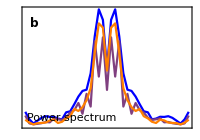

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAc,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSkew,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspec,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

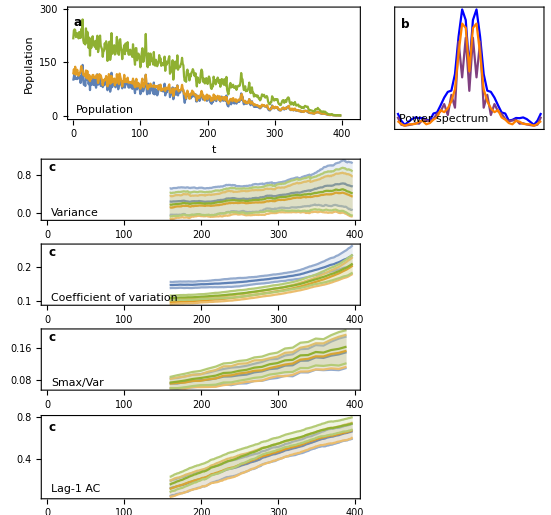

```mathematica
plotGrid
```

```mathematica
(*Export["figures/intervals_"<>simName<>".png",plotGrid,ImageResolution->100];*)
```